This first line will get the relevant data from a CloudObject and save it into "inspections".  The dataset here is large enough that it may take sever minutes to download it so I recommend saving it locally.

```mathematica
buildingPermits=CloudGet[CloudObject[]];
```

```mathematica
Length[buildingPermits]
```

253391

```mathematica
sample = RandomSample[buildingPermits,500]
```

column1 | WORKTYPE | PermitTypeDescr | DESCRIPTION | Comments | APPLICANT | DECLARED_VALUATION | TOTAL_FEES | ISSUED_DATE | EXPIRATION_DATE | STATUS | OWNER | OCCUPANCYTYPE | Sq_feet | ADDRESS | CITY | STATE | ZIP | Property_ID | Parcel_ID | Location
SF170796 | INTREN | Short Form Bldg Permit | Renovations -Interior  NSC | Supply all labor and materials to renovate existing men's and ladies locker rooms on the 8th floor. Replace existing door and frame  metal lockers  millwork light fixtures plumbing fixtures and ceilings.Relocate existing lighting  ductwork diffusers and sprinkers to accomodate new ceiling layout.Patch all walls and paint. Repair existing flooring. | Thomas Caulfield | 181 173.00 $ | 1 840.00 $ | 8 Aug 2012 11:08:07 | 8 Feb 2013 00:00:00 | EXPIRED | CONSTITUTION OF | Comm | 0 | 149     Thirteenth ST | Charleston | Massachusetts, United States | 2129 | 135562 | 203510451 | GeoPosition[{42.3775,-71.052}]
G44504 | GAS | Gas Permit | Gas | stove and dryer | EDMOND MURPHY | 500.00 $ | 30.00 $ | 27 Sep 2010 14:46:19 | 27 Mar 2011 00:00:00 | EXPIRED | RADOSEVIC  BROOKE  & BRENDAN FULLA | 1-2FAM | 0 | 343    K ST | Unrecognized | Massachusetts, United States | 2127 | 80601 | 702168000 | GeoPosition[{42.332,-71.0375}]
SF318299 | INSUL | Short Form Bldg Permit | Insulation | insulation of the exterior walls and attic with blown in cellulose | A J Michael Casanova | 6 577.00 $ | 90.00 $ | 21 Jan 2014 11:43:01 | 21 Jul 2014 00:00:00 | EXPIRED | PANALAL  MARINA  & ROBINDRA | 1-2FAM | 0 | 142    Ballou AV | Unrecognized | Massachusetts, United States | 2124 | 8018 | 1403793000 | GeoPosition[{42.2837,-71.084}]
ALT418924 | INTREN | Long Form/Alteration Permit | Renovations -Interior  NSC | - Change finished attic into legal extended living space. - Alter Attic Stairway into legal access of of ""Master Suite Bedroom with Bath.(This includes taking down a wall around a chimney. - Alter kitchen window to allow for added kitchen counter space - Remove wall seperating kitchen and dining room and install header in place. - Construct 2 closets in master Suite Attic bedroom. - Master suite bedroom demo to widen opening seperating rooms. |  | 5 000.00 $ | 118.00 $ | 4 Dec 2014 09:01:06 | 4 Jun 2015 00:00:00 | EXPIRED | FULCAR  ROBERT | 1-2FAM | 1300 | 55    Navarre ST | Unrecognized | Massachusetts, United States | 2131 | 100424 | 1806717000 | GeoPosition[{42.2766,-71.1175}]
SF460174 | RAZE | Short Form Bldg Permit | Removal of structure | Complete demolition of existing structure | CHAD VINCENT | 40 000.00 $ | 420.00 $ | 6 Apr 2015 14:25:53 | 6 Oct 2015 00:00:00 | EXPIRED | THIRTY 7- 45 BABSON ST LLC | Comm | 0 | 37   Babson St | Unrecognized | Massachusetts, United States | 2126 | 7444 | 1800966000 | GeoPosition[{42.2751,-71.0926}]
SF391284 | OTHER | Short Form Bldg Permit | Other | NSTAR HIGH VOLTAGE SUB STATION 71. INTERIOR IMPROVENETS UNDER THE JURISTION OF MASS DEPARTEMT OF PUBLIC UTILITIES. ALL WORK WILL BE IN COMPLIANCE WITH 780CMR  527CMR. THIS IS SECURE HIGH VOLTAGE ELCETRICAL FACILITY. NO PUBLIC OR UNTRAINED PERRSONNEL ACCESS. | Jack Moriarty | 50 000.00 $ | 520.00 $ | 4 Aug 2014 12:22:56 | 4 Feb 2015 00:00:00 | EXPIRED | INTERCONTINENTA | Comm | 0 | 41-43   Hawkins ST | Boston | Massachusetts, United States | 2114 | 71504 | 302644000 | GeoPosition[{42.3622,-71.0609}]
ETS295754 | TMPSER | Electrical Temporary Service | Temporary Service | Temporary generator power and electrical distribution to power guard shack in parking lot adjacent to Boston Beer Works. | Jeff Antonellis | 2 000.00 $ | 35.00 $ | 17 Oct 2013 10:56:44 | 17 Apr 2014 00:00:00 | EXPIRED | SLESAR BROS BREWING CO INC | Comm | 0 | 61-65   Brookline AV | Boston | Massachusetts, United States | 2215 | 22107 | 2100065000 | GeoPosition[{42.3472,-71.099}]
SF382034 | EXTREN | Short Form Bldg Permit | Renovations - Exterior | Replace and repair concrete walk | Gregory Smith | 8 850.00 $ | 110.00 $ | 9 Jul 2014 12:01:22 | 9 Jan 2015 00:00:00 | EXPIRED | THE WINSOR SCHOOL | Other | 0 | 103-117   Pilgrim RD | Boston | Massachusetts, United States | 2215 | 110326 | 401997000 | GeoPosition[{42.3409,-71.1071}]
ALT87166 | INTREN | Long Form/Alteration Permit | Renovations -Interior  NSC | Renovation of existing classroom to include new HVAC  electrical  plumbing  rough carpentry  millwork and ACT ceilings. Work to completed on 1st floor. | Kevin Caggiano | 210 000.00 $ | 2 562.00 $ | 14 Nov 2011 11:21:20 | 14 May 2012 00:00:00 | EXPIRED | D.B.A: Facilities & Operations | Comm | 10000 | 260   Longwood Av | Boston | Massachusetts, United States | 2115 | 157056 | 401882000 | GeoPosition[{42.337,-71.1042}]
E38995 | SRVCHG | Electrical Permit | Service Change | Office building. Existing tenant expansion first  second and third floors. new service for elevator | PHILLIP OSTROW | 20 000.00 $ | 92.50 $ | 18 Aug 2010 15:27:59 | 18 Feb 2011 00:00:00 | EXPIRED | CHANNEL CENTER | Comm | 0 | 20     Channel Center ST | Boston | Massachusetts, United States | 2127 | 28853 | 602757040 | GeoPosition[{42.3457,-71.0518}]
G80990 | GAS | Gas Permit | Gas | gas connection for lochinvar hot water boiler | PATRICK CORCORAN | 5 000.00 $ | 200.00 $ | 23 Jun 2011 09:03:00 | 23 Dec 2011 00:00:00 | EXPIRED | METROPOLITAN RE | 7More | 0 | 1    Nassau ST | Boston | Massachusetts, United States | 2111 | 100246 | 305424030 | GeoPosition[{42.3486,-71.063}]
PL207377 | PLUMBING | Plumbing Permit | Plumbing | Installing third floor master bath with laundry | JUSTIN PAUQUETTE | 3 500.00 $ | 40.00 $ | 12 Dec 2012 11:38:44 | 12 Jun 2013 00:00:00 | EXPIRED | JENNINGS  WILLIAM E | 1-2FAM | 2500 | 193     Grampian WY | Unrecognized | Massachusetts, United States | 2125 | 65680 | 1302494000 | GeoPosition[{42.3096,-71.0502}]
SF410720 | SOL | Short Form Bldg Permit | Solar Panels | Install Solar Electric panels on roof of existing home  to be interconnected with the home's Electrical System. [JB-0212608-00] | SolarCity Corp | 12 000.00 $ | 140.00 $ | 17 Oct 2014 18:48:55 | 17 Apr 2015 00:00:00 | EXPIRED | TSENG HSUE H-CH | 1-2FAM | 0 | 16    Hollywood RD | Unrecognized | Massachusetts, United States | 2132 | 74739 | 2004038000 | GeoPosition[{42.296,-71.1491}]
ELV180535 | ELECTRICAL | Electrical Low Voltage | Electrical | Install residential security system. | Paul Delsignor | 400.00 $ | 30.00 $ | 5 Sep 2012 11:42:36 | 5 Mar 2013 00:00:00 | EXPIRED | CABRERA  LELIA | 1-2FAM | 0 | 7    Weld AV | Unrecognized | Massachusetts, United States | 2119 | 147039 | 1101542000 | GeoPosition[{42.315,-71.0984}]
SF230130 | INTEXT | Short Form Bldg Permit | Interior/Exterior Work | Install new windows front and rear of bldge. | STEVEN SILVERMAN | 16 000.00 $ | 180.00 $ | 26 Mar 2013 12:52:45 | 26 Sep 2013 00:00:00 | EXPIRED | 170 SAINT BOTOLPH ST REALTY TRUST | Multi | 0 | 170    Saint Botolph ST | Boston | Massachusetts, United States | 2115 | 120728 | 402369000 | GeoPosition[{42.3428,-71.0831}]
E113228 | ELECTRICAL | Electrical Permit | Electrical | Install lighting and power for new office space. | James Green | 20 000.00 $ | 102.00 $ | 9 Jan 2012 08:35:36 | 9 Jul 2012 00:00:00 | EXPIRED | RP BEAL ONE OWN | Comm | 0 | 451     D ST | Boston | Massachusetts, United States | 2210 | 45546 | 602825000 | GeoPosition[{42.3452,-71.042}]
⋮_484 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
2 levels | 500rows |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | Dataset[{__Association}]

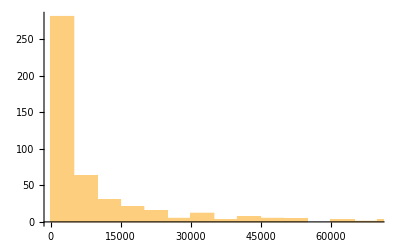

```mathematica
sample[Histogram, "DECLARED_VALUATION"]
```

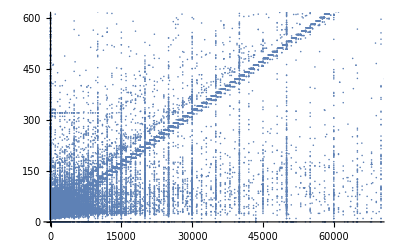

```mathematica
RandomSample[buildingPermits,100000][ListPlot,{"DECLARED_VALUATION","TOTAL_FEES"}]
```

```mathematica
RandomSample[buildingPermits,1000][(FindFit[#,m*x+b,{m,b},x]&),{"DECLARED_VALUATION","TOTAL_FEES"}/*Values/*QuantityMagnitude]
```

{ m→0.000906759,b→291.39 }
1 level | 2elementsDataset[{_, _}]

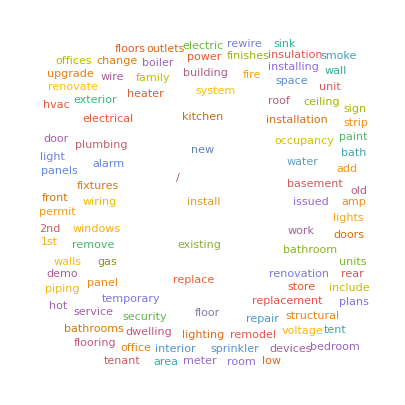

```mathematica
RandomSample[buildingPermits,1000][ToLowerCase/*TextWords/*Flatten/*DeleteStopwords/*WordCloud,"Comments"]
```

```mathematica
buildingPermits[DeleteDuplicates/*DeleteMissing,"Location"]
```

{ GeoPosition[{42.3147,-71.0524}],GeoPosition[{42.3588,-71.0562}],GeoPosition[{42.2876,-71.1191}],GeoPosition[{42.2963,-71.1569}],GeoPosition[{42.263,-71.1592}],GeoPosition[{42.3444,-71.0448}],GeoPosition[{42.3267,-71.0755}],GeoPosition[{42.3432,-71.0736}],GeoPosition[{42.2692,-71.1687}],GeoPosition[{42.3224,-71.0945}],GeoPosition[{42.2735,-71.1277}],GeoPosition[{42.2869,-71.1586}],⋯_51837 }
1 level | 51849elementsDataset[{__GeoPosition}]

```mathematica
RandomSample[buildingPermits,1000][GeoListPlot,"Location"]
```

-Graphics-

```mathematica
buildingPermits[DeleteDuplicates/*DeleteMissing/*(RandomSample[#,1000]&)/*GeoListPlot,"Location"]
```

-Graphics-

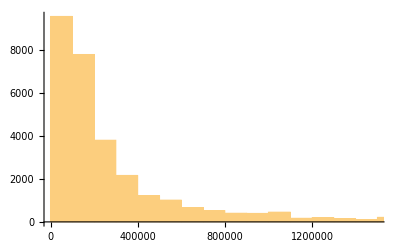

```mathematica
buildingPermits[Query[Select[#>Quantity[50000, "USDollars"]&]]/*Histogram,"DECLARED_VALUATION"]
```

```mathematica
buildingPermits[QuantityMagnitude/*(Ordering[#,-1]&),"DECLARED_VALUATION"]
```

{ 81333 }
1 level | 1elementsDataset[{_Integer}]

```mathematica
buildingPermits[81333]
```

column1 | SF119339
WORKTYPE | COB
PermitTypeDescr | Short Form Bldg Permit
DESCRIPTION | City of Boston
Comments | selective demolition  masonry  concrete new jail cells  gypsum board assemblies  painting  misc metal  skylight framing and glazing plumbing  electric Havc  polymer flooring  roofing
APPLICANT | Michael  Auriemma
DECLARED_VALUATION | 1.831615075e9 $
TOTAL_FEES | 0.00 $
ISSUED_DATE | 14 Feb 2012 09:04:42
EXPIRATION_DATE | 14 Aug 2012 00:00:00
STATUS | EXPIRED
OWNER | 
OCCUPANCYTYPE | Other
Sq_feet | 0
ADDRESS | 40     GIBSON ST
CITY | Unrecognized
⋮_5 | 
1 level | 21elements | Dataset[<|"column1" -> _, "WORKTYPE" -> _, "PermitTypeDescr" -> _, "DESCRIPTION" -> _, "Comments" -> _, "APPLICANT" -> _, "DECLARED_VALUATION" -> _, "TOTAL_FEES" -> _, "ISSUED_DATE" -> _, "EXPIRATION_DATE" -> _, "STATUS" -> _, "OWNER" -> _, "OCCUPANCYTYPE" -> _, "Sq_feet" -> _, "ADDRESS" -> _, "CITY" -> _, "STATE" -> _, "ZIP" -> _, "Property_ID" -> _, "Parcel_ID" -> _, "Location" -> _|>]

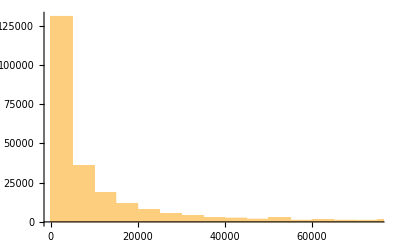

```mathematica
buildingPermits[Histogram,"DECLARED_VALUATION"]
```

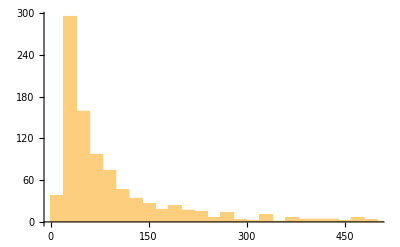

```mathematica
RandomSample[buildingPermits,1000][Histogram,"TOTAL_FEES"]
```

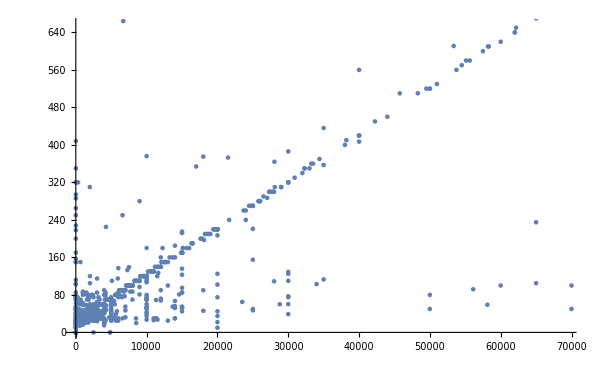

```mathematica
RandomSample[buildingPermits,1000][ListPlot,{"DECLARED_VALUATION","TOTAL_FEES"}]
```

```mathematica
RandomSample[buildingPermits,1000][(FindFit[#,m*x+b,{m,b},x]&),{"DECLARED_VALUATION","TOTAL_FEES"}/*Values/*QuantityMagnitude]
```

{ m→0.00885232,b→-375.475 }
1 level | 2elementsDataset[{_, _}]

```mathematica
1/0.008852319274312759
```

112.965

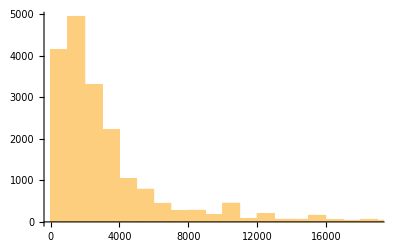

```mathematica
RandomSample[buildingPermits,100000][DeleteCases[0]/*Histogram,"Sq_feet"]
```

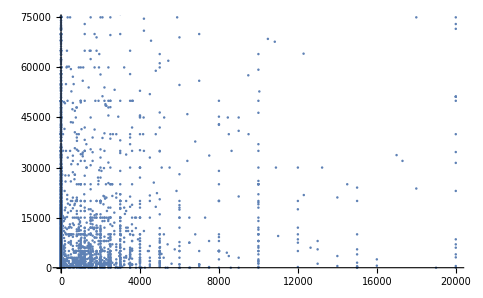

```mathematica
RandomSample[buildingPermits,10000][ListPlot[#,PlotRange->{{0,20000},Automatic}]&,{"Sq_feet","DECLARED_VALUATION"}]
```

```mathematica
occupancies=buildingPermits[GroupBy[ToLowerCase@#["OCCUPANCYTYPE"]&]/*KeySort]
```

| { \[LeftAssociation] column1→G1422,WORKTYPE→GAS,PermitTypeDescr→Gas Permit,⋯_18 \[RightAssociation],⋯_3608 }
1-2fam | { \[LeftAssociation] column1→SF1031,WORKTYPE→OTHER,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_76657 }
1-3fam | { \[LeftAssociation] column1→U497392,WORKTYPE→CONVRT,PermitTypeDescr→Use of Premises,⋯_18 \[RightAssociation],⋯_25441 }
1-4fam | { \[LeftAssociation] column1→E1059,WORKTYPE→SRVCHG,PermitTypeDescr→Electrical Permit,⋯_18 \[RightAssociation],⋯_7011 }
1-7fam | { \[LeftAssociation] column1→E1248,WORKTYPE→ELECTRICAL,PermitTypeDescr→Electrical Permit,⋯_18 \[RightAssociation],⋯_2098 }
1unit | { \[LeftAssociation] column1→SF1035,WORKTYPE→INTREN,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_6220 }
2unit | { \[LeftAssociation] column1→SF1226,WORKTYPE→INTREN,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_634 }
3unit | { \[LeftAssociation] column1→ELV1578,WORKTYPE→LVOLT,PermitTypeDescr→Electrical Low Voltage,⋯_18 \[RightAssociation],⋯_738 }
4unit | { \[LeftAssociation] column1→SF2271,WORKTYPE→INTEXT,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_383 }
5unit | { \[LeftAssociation] column1→E3404,WORKTYPE→ELECTRICAL,PermitTypeDescr→Electrical Permit,⋯_18 \[RightAssociation],⋯_285 }
6unit | { \[LeftAssociation] column1→ALT9507,WORKTYPE→CONVRT,PermitTypeDescr→Long Form/Alteration Permit,⋯_18 \[RightAssociation],⋯_313 }
7more | { \[LeftAssociation] column1→SF1049,WORKTYPE→OTHER,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_4754 }
7unit | { \[LeftAssociation] column1→G1521,WORKTYPE→GAS,PermitTypeDescr→Gas Permit,⋯_18 \[RightAssociation],⋯_75 }
comm | { \[LeftAssociation] column1→ALT8484,WORKTYPE→CONVRT,PermitTypeDescr→Long Form/Alteration Permit,⋯_18 \[RightAssociation],⋯_80516 }
mixed | { \[LeftAssociation] column1→SF1039,WORKTYPE→INTEXT,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_9378 }
multi | { \[LeftAssociation] column1→E1209,WORKTYPE→INTREN,PermitTypeDescr→Electrical Permit,⋯_18 \[RightAssociation],⋯_23320 }
⋮_2 | 
3 levels | 18rows | Dataset[Association[(_String -> _List)..]]

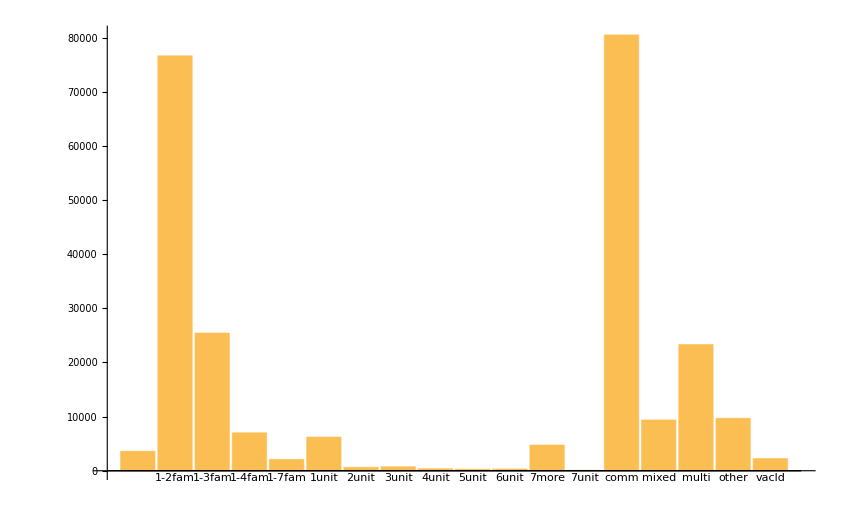

```mathematica
occupancies[KeyValueMap[Labeled[#2,#1]&]/*BarChart,Length]
```

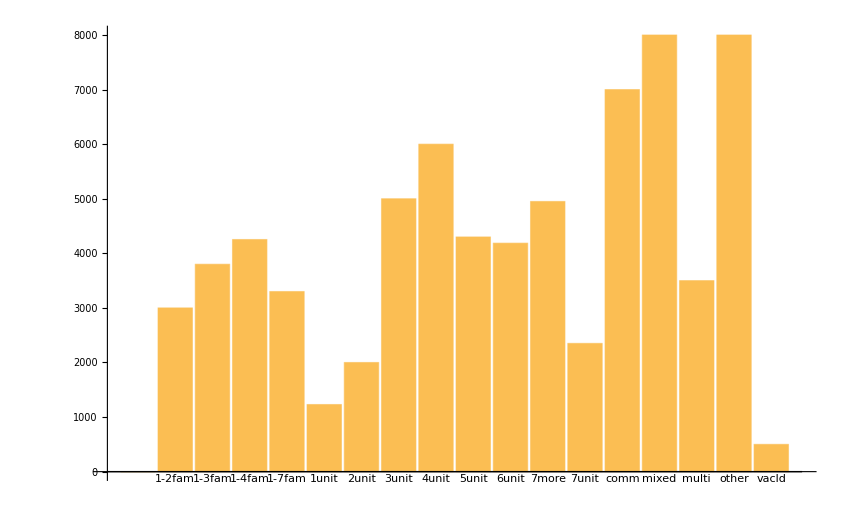

```mathematica
occupancies[KeyValueMap[Labeled[#2,#1]&]/*BarChart,Median,"DECLARED_VALUATION"/*QuantityMagnitude]
```

```mathematica
permitTypes=buildingPermits[GroupBy["PermitTypeDescr"]/*SortBy[-Length[#]&]]
```

Short Form Bldg Permit | { \[LeftAssociation] column1→SF1031,WORKTYPE→OTHER,PermitTypeDescr→Short Form Bldg Permit,⋯_18 \[RightAssociation],⋯_69284 }
Electrical Permit | { \[LeftAssociation] column1→E1051,WORKTYPE→INTREN,PermitTypeDescr→Electrical Permit,⋯_18 \[RightAssociation],⋯_52827 }
Plumbing Permit | { \[LeftAssociation] column1→PL1146,WORKTYPE→PLUMBING,PermitTypeDescr→Plumbing Permit,⋯_18 \[RightAssociation],⋯_34339 }
Gas Permit | { \[LeftAssociation] column1→G1045,WORKTYPE→GAS,PermitTypeDescr→Gas Permit,⋯_18 \[RightAssociation],⋯_26169 }
Electrical Low Voltage | { \[LeftAssociation] column1→ELV1108,WORKTYPE→LVOLT,PermitTypeDescr→Electrical Low Voltage,⋯_18 \[RightAssociation],⋯_21914 }
Long Form/Alteration Permit | { \[LeftAssociation] column1→ALT8484,WORKTYPE→CONVRT,PermitTypeDescr→Long Form/Alteration Permit,⋯_18 \[RightAssociation],⋯_17147 }
Electrical Fire Alarms | { \[LeftAssociation] column1→EFA1050,WORKTYPE→FA,PermitTypeDescr→Electrical Fire Alarms,⋯_18 \[RightAssociation],⋯_13105 }
Certificate of Occupancy | { \[LeftAssociation] column1→COO1011,WORKTYPE→,PermitTypeDescr→Certificate of Occupancy,⋯_18 \[RightAssociation],⋯_8921 }
Electrical Temporary Service | { \[LeftAssociation] column1→ETS3351,WORKTYPE→ELECTRICAL,PermitTypeDescr→Electrical Temporary Service,⋯_18 \[RightAssociation],⋯_3887 }
Excavation Permit | { \[LeftAssociation] column1→EXCA-440515,WORKTYPE→Service,PermitTypeDescr→Excavation Permit,⋯_18 \[RightAssociation],⋯_2274 }
Amendment to a Long Form | { \[LeftAssociation] column1→A2139,WORKTYPE→SITE,PermitTypeDescr→Amendment to a Long Form,⋯_18 \[RightAssociation],⋯_1719 }
Erect/New Construction | { \[LeftAssociation] column1→ERT13148,WORKTYPE→COB,PermitTypeDescr→Erect/New Construction,⋯_18 \[RightAssociation],⋯_1012 }
Use of Premises | { \[LeftAssociation] column1→U497392,WORKTYPE→CONVRT,PermitTypeDescr→Use of Premises,⋯_18 \[RightAssociation],⋯_728 }
Foundation Permit | { \[LeftAssociation] column1→FND41408,WORKTYPE→ERECT,PermitTypeDescr→Foundation Permit,⋯_18 \[RightAssociation],⋯_51 }
3 levels | 14rows | Dataset[Association[(_String -> _List)..]]

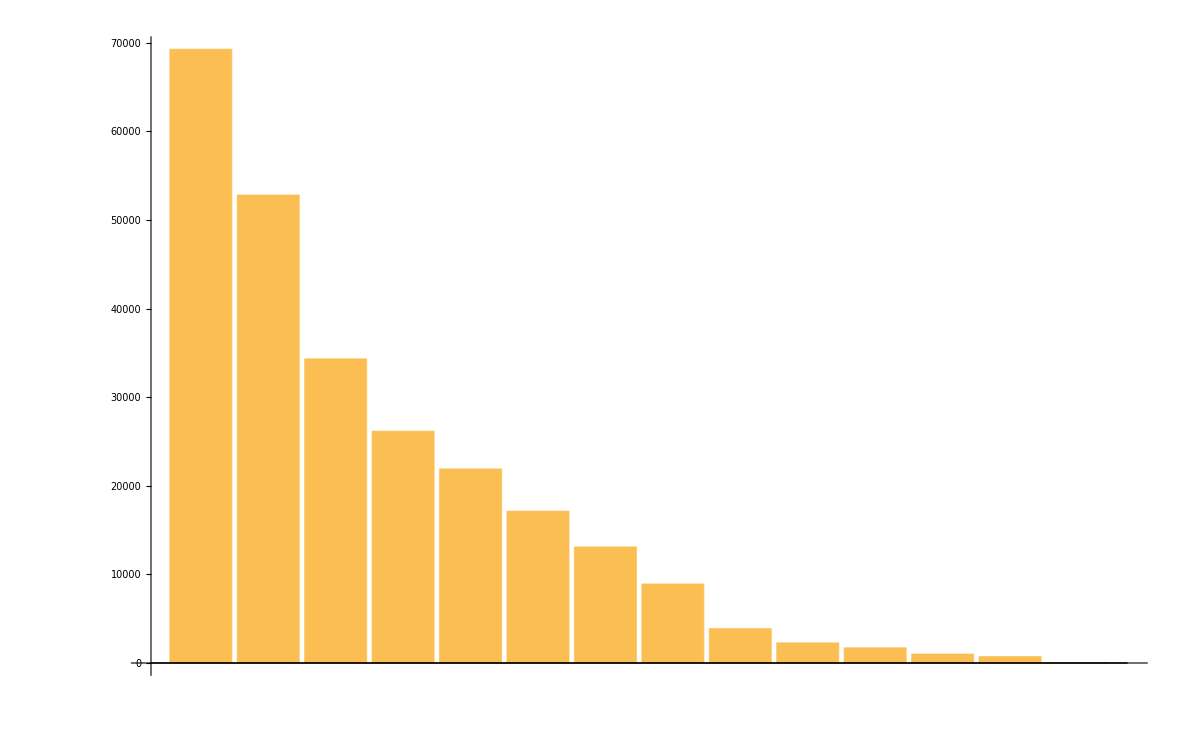

```mathematica
permitTypes[KeyValueMap[Tooltip[#2,#1]&]/*BarChart,Length]
```

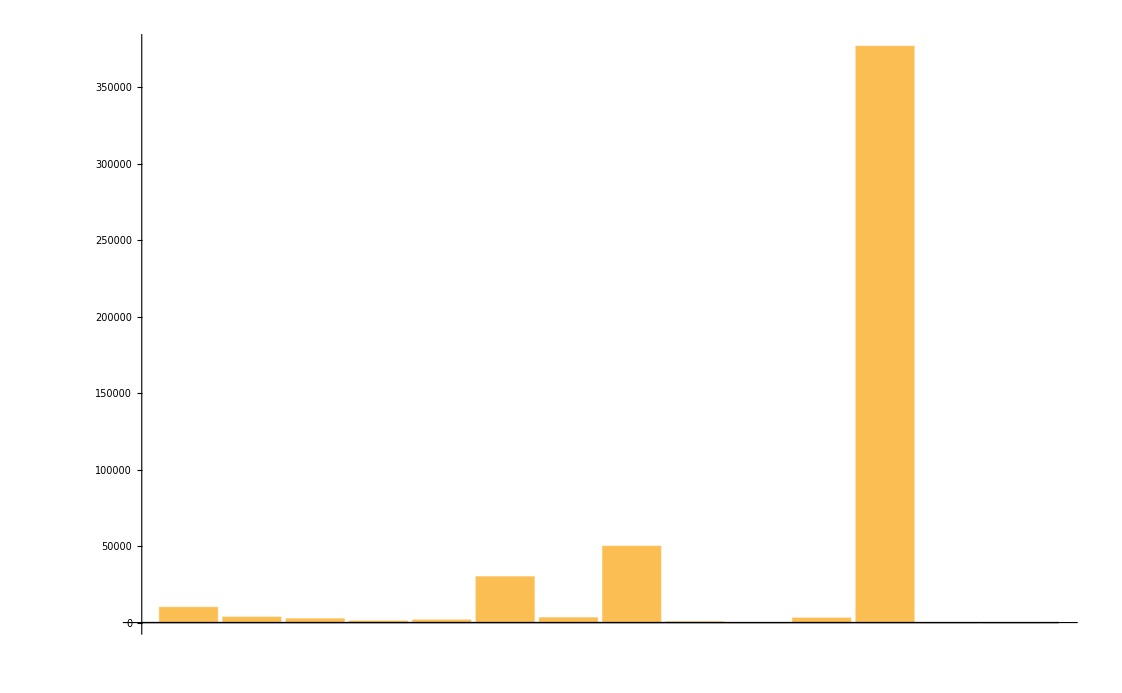

```mathematica
permitTypes[KeyValueMap[Tooltip[#2,#1]&]/*BarChart,Median,"DECLARED_VALUATION"/*QuantityMagnitude]
```

```mathematica
permitTypes["Erect/New Construction"/*GeoListPlot,DeleteDuplicates/*DeleteMissing,"Location"]
```

-Graphics-

```mathematica
permitTypes[All,DeleteDuplicates/*DeleteMissing,"Location"]
```

Short Form Bldg Permit | { GeoPosition[{42.263,-71.1592}],GeoPosition[{42.3444,-71.0448}],GeoPosition[{42.3267,-71.0755}],GeoPosition[{42.3432,-71.0736}],GeoPosition[{42.2692,-71.1687}],GeoPosition[{42.3778,-71.0506}],GeoPosition[{42.347,-71.0715}],GeoPosition[{42.358,-71.0674}],GeoPosition[{42.3116,-71.0845}],GeoPosition[{42.3555,-71.0614}],⋯_33783 }
Electrical Permit | { GeoPosition[{42.3576,-71.0683}],GeoPosition[{42.3398,-71.1057}],GeoPosition[{42.3004,-71.0756}],GeoPosition[{42.3536,-71.0599}],GeoPosition[{42.339,-71.1042}],GeoPosition[{42.3459,-71.1502}],GeoPosition[{42.3505,-71.0886}],GeoPosition[{42.3063,-71.1062}],GeoPosition[{42.3561,-71.0575}],GeoPosition[{42.2848,-71.0628}],⋯_22095 }
Plumbing Permit | { GeoPosition[{42.3407,-71.158}],GeoPosition[{42.3517,-71.1736}],GeoPosition[{42.3171,-71.1056}],GeoPosition[{42.3361,-71.1075}],GeoPosition[{42.2859,-71.1219}],GeoPosition[{42.3046,-71.0677}],GeoPosition[{42.2781,-71.0681}],GeoPosition[{42.3528,-71.1719}],GeoPosition[{42.3779,-71.0659}],GeoPosition[{42.2914,-71.0549}],⋯_19438 }
Gas Permit | { GeoPosition[{42.3224,-71.0945}],GeoPosition[{42.2735,-71.1277}],GeoPosition[{42.2869,-71.1586}],GeoPosition[{42.3061,-71.0652}],GeoPosition[{42.331,-71.1042}],GeoPosition[{42.3087,-71.1056}],GeoPosition[{42.2783,-71.1485}],GeoPosition[{42.3407,-71.158}],GeoPosition[{42.3055,-71.0661}],GeoPosition[{42.2793,-71.0805}],⋯_18318 }
Electrical Low Voltage | { GeoPosition[{42.3448,-71.0904}],GeoPosition[{42.3351,-71.0547}],GeoPosition[{42.3282,-71.0601}],GeoPosition[{42.3544,-71.0622}],GeoPosition[{42.3506,-71.0797}],GeoPosition[{42.3662,-71.0607}],GeoPosition[{42.3588,-71.0618}],GeoPosition[{42.3439,-71.099}],GeoPosition[{42.3671,-71.1219}],GeoPosition[{42.3429,-71.0726}],⋯_8996 }
Long Form/Alteration Permit | { GeoPosition[{42.3588,-71.0562}],GeoPosition[{42.2876,-71.1191}],GeoPosition[{42.3593,-71.0575}],GeoPosition[{42.3594,-71.0511}],GeoPosition[{42.3561,-71.0541}],GeoPosition[{42.3585,-71.0608}],GeoPosition[{42.3648,-71.0538}],GeoPosition[{42.3518,-71.0614}],GeoPosition[{42.3665,-71.0328}],GeoPosition[{42.351,-71.0713}],⋯_8223 }
Electrical Fire Alarms | { GeoPosition[{42.3714,-71.0408}],GeoPosition[{42.3398,-71.1057}],GeoPosition[{42.3557,-71.0582}],GeoPosition[{42.3459,-71.0645}],GeoPosition[{42.3548,-71.0631}],GeoPosition[{42.3638,-71.0617}],GeoPosition[{42.3271,-71.1006}],GeoPosition[{42.3297,-71.0915}],GeoPosition[{42.3423,-71.0518}],GeoPosition[{42.3737,-71.0356}],⋯_5809 }
Certificate of Occupancy | { GeoPosition[{42.2963,-71.1569}],GeoPosition[{42.3518,-71.0699}],GeoPosition[{42.3816,-71.0175}],GeoPosition[{42.3393,-71.0941}],GeoPosition[{42.3755,-71.0609}],GeoPosition[{42.3325,-71.0423}],GeoPosition[{42.2946,-71.0702}],GeoPosition[{42.3435,-71.0748}],GeoPosition[{42.2833,-71.0559}],GeoPosition[{42.3747,-71.0407}],⋯_4077 }
Electrical Temporary Service | { GeoPosition[{42.3429,-71.0537}],GeoPosition[{42.3817,-71.0645}],GeoPosition[{42.2936,-71.0681}],GeoPosition[{42.2913,-71.0764}],GeoPosition[{42.36,-71.0562}],GeoPosition[{42.3213,-71.0457}],GeoPosition[{42.3507,-71.0699}],GeoPosition[{42.3519,-71.1189}],GeoPosition[{42.3226,-71.1011}],GeoPosition[{42.3469,-71.0342}],⋯_972 }
Excavation Permit | { GeoPosition[{42.3503,-71.0895}],GeoPosition[{42.287,-71.045}],GeoPosition[{42.347,-71.1402}],GeoPosition[{42.2999,-71.0739}],GeoPosition[{42.3243,-71.0694}],GeoPosition[{42.3633,-71.1357}],GeoPosition[{42.3804,-71.0397}],GeoPosition[{42.3533,-71.0563}],GeoPosition[{42.3563,-71.0527}],GeoPosition[{42.2408,-71.143}],⋯_1696 }
Amendment to a Long Form | { GeoPosition[{42.3417,-71.0914}],GeoPosition[{42.3427,-71.0693}],GeoPosition[{42.2995,-71.0561}],GeoPosition[{42.3479,-71.1515}],GeoPosition[{42.2651,-71.1504}],GeoPosition[{42.265,-71.1503}],GeoPosition[{42.2652,-71.1505}],GeoPosition[{42.332,-71.046}],GeoPosition[{42.3281,-71.0805}],GeoPosition[{42.359,-71.0579}],⋯_1008 }
Erect/New Construction | { GeoPosition[{42.2892,-71.1614}],GeoPosition[{42.2493,-71.1409}],GeoPosition[{42.2537,-71.1243}],GeoPosition[{42.2727,-71.1623}],GeoPosition[{42.3346,-71.0305}],GeoPosition[{42.3307,-71.0406}],GeoPosition[{42.3212,-71.084}],GeoPosition[{42.2859,-71.1283}],GeoPosition[{42.3349,-71.0504}],GeoPosition[{42.2933,-71.17}],⋯_353 }
Use of Premises | { GeoPosition[{42.3147,-71.0524}],GeoPosition[{42.2862,-71.0447}],GeoPosition[{42.3315,-71.0409}],GeoPosition[{42.251,-71.133}],GeoPosition[{42.302,-71.0539}],GeoPosition[{42.3321,-71.0362}],GeoPosition[{42.2884,-71.1257}],GeoPosition[{42.2914,-71.0684}],GeoPosition[{42.2817,-71.0647}],GeoPosition[{42.3319,-71.0504}],⋯_520 }
Foundation Permit | { GeoPosition[{42.3044,-71.0595}],GeoPosition[{42.3327,-71.092}],GeoPosition[{42.3196,-71.1007}],GeoPosition[{42.3362,-71.0429}],GeoPosition[{42.3159,-71.101}],GeoPosition[{42.3277,-71.0927}],GeoPosition[{42.3166,-71.0469}],GeoPosition[{42.3305,-71.0367}],GeoPosition[{42.3366,-71.0356}],GeoPosition[{42.3831,-71.0154}],⋯_7 }
2 levels | 14rows | Dataset[Association[(_String -> _List)..]]

```mathematica
permitTypes[(GeoListPlot[Values[#],PlotLegends->Keys[#]]&),DeleteDuplicates/*DeleteMissing/*(RandomSample[#,UpTo[Round[Length[#]*0.007]]]&),"Location"]
```

-Graphics-

```mathematica
occupancies[(GeoListPlot[Values[#],PlotLegends->Keys[#]]&),DeleteDuplicates/*DeleteMissing/*(RandomSample[#,UpTo[Round[Length[#]*0.007]]]&),"Location"]
```

-Graphics-

```mathematica
permitTypeMap=Normal@buildingPermits[Union/*MapIndexed[#1->First[#2]&]/*Association,"PermitTypeDescr"/*ToLowerCase]
```

<|amendment to a long form→1,certificate of occupancy→2,electrical fire alarms→3,electrical low voltage→4,electrical permit→5,electrical temporary service→6,erect/new construction→7,excavation permit→8,foundation permit→9,gas permit→10,long form/alteration permit→11,plumbing permit→12,short form bldg permit→13,use of premises→14|>

```mathematica
occTypeMap=Normal@buildingPermits[Union/*MapIndexed[#1->First[#2]&]/*Association,"OCCUPANCYTYPE"/*ToLowerCase]
```

<|→1,1-2fam→2,1-3fam→3,1-4fam→4,1-7fam→5,1unit→6,2unit→7,3unit→8,4unit→9,5unit→10,6unit→11,7more→12,7unit→13,comm→14,mixed→15,multi→16,other→17,vacld→18|>

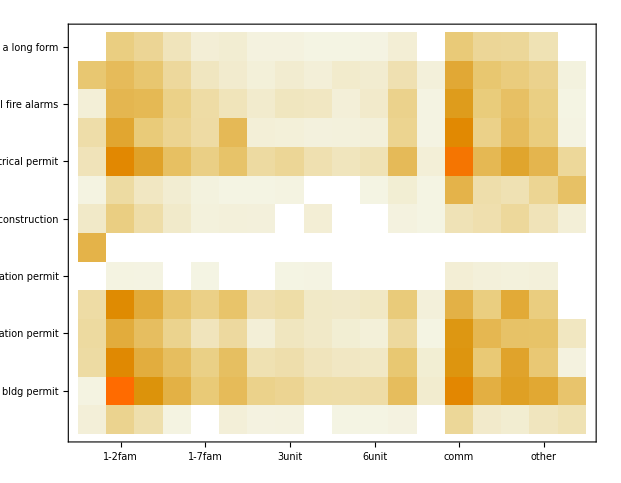

```mathematica
buildingPermits[Counts/*Normal/*SparseArray/*(MatrixPlot[#,FrameTicks->{Reverse/@List@@@Normal@permitTypeMap,{#1,Rotate[#2,Pi/2]}&@@@Reverse/@List@@@Normal@occTypeMap,None,None}]&),{"PermitTypeDescr","OCCUPANCYTYPE"}/*({Replace[ToLowerCase@#["PermitTypeDescr"],permitTypeMap],Replace[ToLowerCase@#["OCCUPANCYTYPE"],occTypeMap]}&)]
```